This notebook contains the code and data necessary to generate the main figures in the paper “Situating the actual within the space of the possible: Parameter space structure and degeneracy in brain-body-environment systems” by Randall D. Beer and Eduardo J. Izquierdo.

First evaluate all cells in the “Initialization.nb” file. Then the components of each figure can be reproduced by evaluating all cells in that figure’s section. Note that some of these evaluations can take a *very* long time.

Randall D. Beer - 7/1/2025

## Figure 3

NOTE: Parameter order in this notebook is  θ_1, θ_2, w_11, w_21, w_12, w_22, τ_1, τ_2 (where w_ij is input from i to j)

### Data

Procedure:
  1) 10,000 evolutionary runs
  2) 1 billion random samples with 0.5 cutoff using extended parameter ranges
  3) Many random samples with increasingly restricted parameter ranges (starting with the 0.5 ranges) and cutoffs

#### 0.6 Data

Data from many random samples

```mathematica
(*Data060 = SanitizeAndReEvaluateData[Data060,0.6];*)
```

```mathematica
Data060=;
```

```mathematica
Length[Data060]
```

18501

```mathematica
MaximalBy[Data060,Last]
```

{{-3.49275,-11.9439,19.1167,-15.0962,11.117,6.04746,0.21859,13.033,0.624262}}

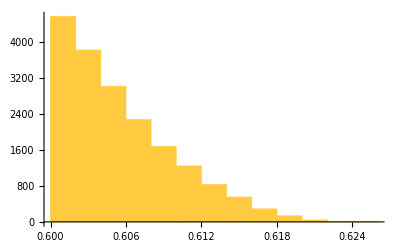

```mathematica
Histogram[Last/@Data060]
```

```mathematica
ParameterRanges[Data060]
```

{{{-4,13},{-24,-1},{2,24},{-24,-5},{1,24},{-9,24},{0,8},{0,15}},{{-24,-6},{-4,21},{1,24},{4,24},{-24,-1},{-15,24},{0,9},{1,15}}}

#### 0.625 Data

Data from many random samples

```mathematica
(*Data0625=SanitizeAndReEvaluateData[Data0625,0.625];*)
```

```mathematica
Data0625=;
```

```mathematica
Length[Data0625]
```

254

```mathematica
MaximalBy[Data0625,Last]
```

{{0.953097,-8.9408,17.0914,-15.8206,6.64919,7.15402,0.101182,13.5054,0.626555}}

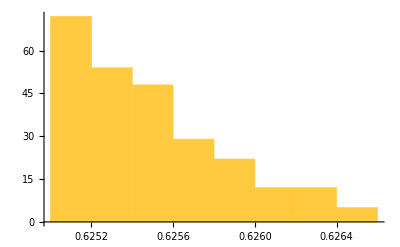

```mathematica
Histogram[Last/@Data0625]
```

```mathematica
ParameterRanges[Data0625]
```

{{{-4,4},{-24,-6},{14,24},{-24,-13},{4,22},{2,24},{0,1},{4,15}},{{-24,-14},{-2,9},{16,24},{11,24},{-24,-4},{2,24},{0,1},{4,15}}}

### Plots

```mathematica
Display2DProjectionGrid[Data060,Data0625]
```

## Figure 4

### Plots

```mathematica
Display3DProjections[Data060,{}]//Quiet
```

```mathematica
Display3DProjections[{},Data0625]//Quiet
```

```mathematica
Show[-Graphics3D-,Graphics3D[{Red,PointSize[0.01],Map[Point[{#[[2]],#[[6]],#[[5]]}]&,Select[Data0625,!((#[[6]]>=4&&RegionMember[ℛ,{#[[2]],#[[6]],#[[5]]}]))&&#[[6]]>4&]]}]]
```

### 0.625 Statistics

#### Neuron 1

```mathematica
Length[Select[Data0625,#[[3]]>=4&&RegionMember[ℛ,{#[[1]],#[[3]],#[[4]]}]&]]/Length[Data0625]
```

1

```mathematica
Length[Select[Data0625,RegionMember[ℛ̃,{#[[1]],#[[3]],#[[4]]}]&]]/Length[Data0625]
```

0

```mathematica
Length[Select[Data0625,!((#[[3]]>=4&&RegionMember[ℛ,{#[[1]],#[[3]],#[[4]]}])||RegionMember[ℛ̃,{#[[1]],#[[3]],#[[4]]}])&]]/Length[Data0625]
```

0

#### Neuron 2

```mathematica
Length[Select[Data0625,#[[6]]>=4&&RegionMember[ℛ,{#[[2]],#[[6]],#[[5]]}]&]]/Length[Data0625]//N
```

0.909449

```mathematica
Length[Select[Data0625,RegionMember[ℛ̃,{#[[2]],#[[6]],#[[5]]}]&]]/Length[Data0625]//N
```

0.0511811

```mathematica
Length[Select[Data0625,!((#[[6]]>=4&&RegionMember[ℛ,{#[[2]],#[[6]],#[[5]]}])||RegionMember[ℛ̃,{#[[2]],#[[6]],#[[5]]}])&]]/Length[Data0625]//N
```

0.0393701

### 0.60 Statistics

#### Neuron 1

```mathematica
Length[Select[Data060,#[[3]]>=4&&RegionMember[ℛ,{#[[1]],#[[3]],#[[4]]}]&]]/Length[Data060]//N
```

0.99773

```mathematica
Length[Select[Data060,RegionMember[ℛ̃,{#[[1]],#[[3]],#[[4]]}]&]]/Length[Data060]//N
```

0.00227015

```mathematica
Length[Select[Data0625,!((#[[3]]>=4&&RegionMember[ℛ,{#[[1]],#[[3]],#[[4]]}])||RegionMember[ℛ̃,{#[[1]],#[[3]],#[[4]]}])&]]/Length[Data0625]
```

0

#### Neuron 2

```mathematica
Length[Select[Data060,#[[6]]>=4&&RegionMember[ℛ,{#[[2]],#[[6]],#[[5]]}]&]]/Length[Data060]//N
```

0.876601

```mathematica
Length[Select[Data060,RegionMember[ℛ̃,{#[[2]],#[[6]],#[[5]]}]&]]/Length[Data060]//N
```

0.106697

```mathematica
Length[Select[Data060,!((#[[6]]>=4&&RegionMember[ℛ,{#[[2]],#[[6]],#[[5]]}])||RegionMember[ℛ̃,{#[[2]],#[[6]],#[[5]]}])&]]/Length[Data060]//N
```

0.0167018

## Figure 5

### Fitness Surface

```mathematica
TT=
Transpose[
ParallelTable[
If[RegionMember[ℛℛ,{Θ1,W11}],CAsymptoticFitness[{θ1->Θ1,w11->W11},250,10,0.005],0],{Θ1,-4,10,0.01},{W11,3,20,0.01},
Method->"CoarsestGrained"]];
```

```mathematica
Show[ListPlot3D[TT,DataRange->{{-4,10},{3,20}},Mesh->False,AxesLabel->{"θ_1","w_11","<v>"},AxesStyle->Black],Graphics3D[{Darker[Green],AbsolutePointSize[6],Point[{-3.21,15.96,0.623}]}]]
```

### Theoretical Boundaries and Internal Structure

```mathematica
SolutionPT={θ1,w11}/.Pis;
ℛPTs=;
ℛTildePTs=;
```

```mathematica
SLPTs=;
SRPTs=;
HPTs=;
BHomPTs=;
SCPTs=;
```

```mathematica
LCMin1PTs=;
LCMax1PTs=;
LCMin2PTs=;
```

```mathematica
R1=;
R2=;
```

```mathematica
MPR=;
```

```mathematica
Show[
Graphics[
{{AbsoluteThickness[1],Dashed,Line[ℛPTs],Line[Drop[ℛTildePTs,22]]},{AbsolutePointSize[0.9],Gray,Point/@MPR},{AbsoluteThickness[1],Red,Line[R1],Blue,Line[R2]},{AbsoluteThickness[1.5],RGBColor[0.880722, 0.611041, 0.142051],Line[SLPTs],Line[SRPTs],RGBColor[0.368417, 0.506779, 0.709798],Line[HPTs],Dashed,Red,Line[BHomPTs],Magenta,Line[SCPTs]},{AbsoluteThickness[1.5],RGBColor[0.7777777777777778, Rational[5, 9], 0.7777777777777778],Line[LCMin1PTs],Line[LCMax1PTs],Line[LCMin2PTs]},{Darker[Green],AbsolutePointSize[6],Point[SolutionPT]}}],PlotRange->{{-3.933348959228002,9.95252807135044},{3.4531247459892036,19.867130445738578}},PlotRangePadding->{{0.2892891048037174,0.28928910480371783},{0.27771754061156884,0.27771754061156884}},PlotRangeClipping->True,
Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{Subscript[θ, 1],Subscript[w, 11]},AspectRatio->1]
```

## Figure 6

### Limit Cycle Space

```mathematica
DisplayLimitCycle[Θ1_?NumberQ,W11_?NumberQ,skip_:25000,MaxPeriod_:10000,tolerance_:0.001]:=
With[{
DS1=DS/.{θ1->Θ1,w11->W11},
DF=Dynamica`Private`DSFunctions[DS]/.{θ1->Θ1,w11->W11}/.Dynamica`Private`DSParameterSubsts[DS]},
Module[{IC,S,T},
IC=({y1[t],y2[t]}/.Trajectory[DS1,{0,0},skip,MaxSteps->Automatic])/.t->skip;
If[AnyTrue[LSPoint/@EquilibriumPoints[DS1],EuclideanDistance[IC,#]<tolerance&],Return[$Failed]];
S=NDSolve[
Join[
Thread[{y1'[t],y2'[t]}==(DF/.{y1->y1[t],y2->y2[t]})],
Thread[{y1[0],y2[0]}==IC],
{WhenEvent[EuclideanDistance[{y1[t],y2[t]},IC]==tolerance&&t>0.1,"StopIntegration","DetectionMethod"->"Interpolation"]}],
{y1[t],y2[t]},
{t,0,MaxPeriod},MaxSteps->Automatic];
T=S[[1,1,2,0]][[1,1,2]];
If[T==MaxPeriod,(*Echo[{Θ1,W11},"Failed to Close"];*)Return[$Failed]];
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,5]]],ToExpression[ToString[SetPrecision[T,5]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed First Time: "];*)LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,6]]],ToExpression[ToString[SetPrecision[T,6]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Second Time: "];*)
LC=FindLimitCycle[DS1,ToExpression[ToString[SetPrecision[IC,7]]],ToExpression[ToString[SetPrecision[T,7]]]];
If[LC===Null,
(*Echo[{Θ1,W11},"FindLimitCycle Failed Third Time, Skipping: "];*)
Return[$Failed]]]];
oDF=Dynamica`Private`DSFunctions[DSo]/.{θ1->Θ1,w11->W11}/.Dynamica`Private`DSParameterSubsts[DS];
ParametricPlot[{σ[y1[t]+Θ1],σ[y2[t]+DSParameterValue[DS,θ2]]}/.LCTrajectory[LC],{t,0,T},PlotPoints->100,PlotStyle->AbsoluteThickness[1.5],
ColorFunction->({x,y}|->ColorData["TemperatureMap"][Norm[oDF/.{o1->x,o2->y}]/3.5]),
ColorFunctionScaling->False,PlotRange->{{-0.02,1.02},{-0.02,1.02}},Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],FrameTicks->None,AspectRatio->1,
Prolog->{RGBColor[0, Rational[2, 3], 0],AbsoluteDashing[{2}],AbsoluteThickness[0.75],Cases[DisplayPhasePortrait[DSo/. {θ1->Θ1,w11->W11},Tries->0,NullManifolds->True,NullManifold2PlotPoints->150],_Line,∞]}]]]
```

```mathematica
LLCSpace={Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[-3,y],{-3,y}},{y,9,17}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[-2,y],{-2,y}},{y,8,17}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[-1,y],{-1,y}},{y,7,16}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[0,y],{0,y}},{y,7,13}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[1,y],{1,y}},{y,6,14}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[2,y],{2,y}},{y,5,13}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[3,y],{3,y}},{y,5,12}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[4,y],{4,y}},{y,4,11}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[5,y],{5,y}},{y,4,10}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[6,y],{6,y}},{y,4,9}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[7,y],{7,y}},{y,4,7}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,ParallelTable[{DisplayLimitCycle[8,y],{8,y}},{y,4,6}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayLimitCycle[9,y],{9,y}},{y,5,5}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,
{{DisplayLimitCycle[-3,17.998],{-3,17.998}},{DisplayLimitCycle[0,6.02],{0,6.02}},{DisplayLimitCycle[0,13.999],{0,13.999}},{DisplayLimitCycle[0,15],{0,15}}}]};
```

```mathematica
Show[G,Graphics[LLCSpace],PlotRange->{{-4,10},{3,20}},AspectRatio->1,Frame->True,FrameLabel->{Subscript[θ, 1],Subscript[w, 11]},FrameStyle->Directive[14,Black],ImageSize->500]
```

### Body Cycle Space

```mathematica
T=;
```

```mathematica
GG=With[{MinP=10,MaxP=45,Δ=0.01},
Show[
Graphics[{Opacity[0.5],ColorData["M10DefaultDensityGradient"][(#[[3]]-MinP)/MaxP],Rectangle[{#[[1]]-Δ/2,#[[2]]-Δ/2},{#[[1]]+Δ/2,#[[2]]+Δ/2}]}&/@T],AspectRatio->1,FrameLabel->{Subscript[θ, 1],Subscript[w, 11]},Frame->True,FrameStyle->Directive[12,Black],PlotRange->{{-4,10},{3,20}},ImageSize->500]]
```

```mathematica
Clear[DisplayBodyCycle]
```

```mathematica
DisplayBodyCycle[Θ1_?NumberQ,W11_?NumberQ,SkipSteps_:1,NumSteps_:1]:=
Module[{S,PTs},
S=QuietEcho[NDSolveStep[{0,0,π/6,0},Join[{θ1->Θ1,w11->W11},Pis]//Echo,SkipSteps,NumSteps]];
If[S===$Failed,Return[$Failed]];
PTs=Map[{#[[4]],#[[5]]}&,S];
Show[
$OG,
Graphics[{Blue,AbsoluteThickness[1.5],Line[Append[PTs,First[PTs]]]}],
PlotRange->{{-0.9947592804475793,0.5235987755982991},{-0.07540269928703086,0.22882280821594225}},AspectRatio->1,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[0.5]],FrameTicks->None]]
```

```mathematica
TT={Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[-3,y],{-3,y}},{y,9,17}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[-2,y],{-2,y}},{y,8,17}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[-1,y],{-1,y}},{y,8,16}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[0,y],{0,y}},{y,7,13}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[1,y],{1,y}},{y,6,14}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[2,y],{2,y}},{y,5,13}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[3,y],{3,y}},{y,5,12}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[4,y],{4,y}},{y,4,11}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[5,y],{5,y}},{y,4,10}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[6,y],{6,y}},{y,4,9}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[7,y],{7,y}},{y,4,7}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[8,y],{8,y}},{y,4,6}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,Table[{DisplayBodyCycle[9,y],{9,y}},{y,5,5}]],
Map[Inset[#[[1]],#[[2]],Center,{1,1}]&,{{DisplayBodyCycle[-3,17.998],{-3,17.998}}(*,{DisplayBodyCycle[0,6.02],{0,6.02}}*),{DisplayBodyCycle[0,13.999],{0,13.999}},{DisplayBodyCycle[0,15],{0,15}}}]};
```

```mathematica
Show[GG,Graphics[TT],PlotRange->{{-4,10},{3,20}},AspectRatio->1,Frame->True,FrameLabel->{Subscript[θ, 1],Subscript[w, 11]},FrameStyle->Directive[14,Black],PlotRange->{{-4,10},{3,20}},ImageSize->500]
```

### Fitness Space

```mathematica
F=Flatten[ParallelTable[{Θ1,W11,If[RegionMember[𝒪,{Θ1,W11}],CAsymptoticFitness[{θ1->Θ1,w11->W11},1000,1,0.005],0]},{Θ1,-4,10,0.01},{W11,3,20,0.01},
Method->"CoarsestGrained"],1];
```

```mathematica
FP=ListDensityPlot[F,InterpolationOrder->0,ColorFunction->ColorData["M10DefaultDensityGradient"],PlotRange->{{-4,10},{3,20}},PlotLegends->True,AspectRatio->1,FrameLabel->{Subscript[θ, 1],Subscript[w, 11]},FrameStyle->Directive[Black,14],ImageSize->500]
```

## Figure 7

### Region Constraint

```mathematica
RBottom=-Graphics3D-;
```

### Functional Stepper Region

```mathematica
FRBottom=-Graphics3D-;
```

```mathematica
FRTop=-Graphics3D-;
```

### Peak

```mathematica
Peak1=;
Peak2=;
```

### Ridges

#### W21 = -24

```mathematica
SR24=DisplaySteppingRegion[-24];
```

```mathematica
SR24B3=Map[Line[{Append[#[[1,1]],-24],Append[#[[1,2]],-24]}]&,Cases[Normal[Show[RegionBoundary[Region[DiscretizeGraphics[SR24]]]]],_Line,∞]];
```

```mathematica
(*FAL=SlicedFALRidge[-24,{{4,35,1},0.001},10,100,Region[DiscretizeGraphics[SR]]];*)
```

```mathematica
(*SlicedFALRidge[-24,{{27.25,27.25,1},0.001},10,100,Region[DiscretizeGraphics[SR]]]*)
```

```mathematica
FAL24={{-3.147481179777513,10.6},{-3.154407180653868,10.7},{-3.162399797626062,10.8},{-3.1791105469507945,11},{-3.262934566850463,12},{-3.3407253517395503,13},{-3.4117985730237548,14},{-3.4765456318005326,15},{-3.5354389055124074,16},{-3.5887367678037316,17},{-3.636561167466115,18},{-3.678807644723845,19},{-3.7149708406526543,20},{-3.7444230393834763,21},{-3.765633786759727,22},{-3.776205743200298,23},{-3.7718803837674786,24},{-3.744453828594059,25},{-3.6757272053501424,26},{-3.6130644662635163,26.5},{-3.569658810642056,26.75},{-3.549116259242729,26.85},{-3.538109026917768,26.9},{-3.5142199440207467,27},{-3.4412239881208864,27.25},{-3.3399732385643057,27.5},{-3.1833354657496047,27.75},{-2.8145326729458393,28},{-2.3396576729458394,28},{-1.6928979657496046,27.75},{-1.259285738564305,27.5},{-0.8819739881208862,27.25},{-0.5339074440207471,27},{-0.40017152691776736,26.9},{-0.33424125924272907,26.85},{-0.22167875924272912,26.85},{-0.05729652691776735,26.9},{0.48551597308223293,26.9},{0.666946240757271,26.85},{0.9099661893579438,26.75},{1.3356855337364841,26.5},{1.9396477946498585,26},{2.4849836714059412,25},{2.8544946162325227,24},{3.2536067567997025,23},{3.6873662132402734,22},{4.149201960616524,21},{4.638654159347346,20},{5.158504855276155,19},{5.713313832533886,18},{6.3091382321962675,17},{6.952686094487594,16},{7.6512668681994676,15},{8.411826426976244,14},{9.240587148260449,13},{10.142127933149535,12},{11.119701953049205,11},{11.324537702373942,10.8},{11.428155319346136,10.7},{11.532581320222487,10.6},{12.17585749858948,10},{13.314351489256335,9},{14.542127017462409,8},{15.873682430879338,7},{18.15626153314242,5.5},{19.047860888096146,5},{19.237559104568312,4.9},{19.430782527980945,4.8},{19.822397360183082,4.6},{20.011753771319427,4.5},{20.173451489151233,4.4}};
```

```mathematica
FAL24$3=Append[#,-24]&/@FAL24;
```

```mathematica
(*ABAL=SlicedABALRidge[-24,{{27.5,27.5,1},0.001},10,Region[DiscretizeGraphics[SR]]];*)
```

```mathematica
(*SlicedABALRidge[-24,{{30.2,30.2,1},0.001},10,100,Region[DiscretizeGraphics[SR]]]*)
```

```mathematica
ABAL24={{-2.7605824617240042,10.5},{-2.7667936797775132,10.6},{-2.7735946806538676,10.7},{-2.7803997976260613,10.8},{-2.7870020675432485,10.9},{-2.7932980469507944,11},{-2.8367470668504637,12},{-2.8537878517395505,13},{-2.855673573023754,14},{-2.8484206318005327,15},{-2.835438905512407,16},{-2.8190492678037318,17},{-2.801686167466115,18},{-2.786370144723845,19},{-2.7773458406526546,20},{-2.7805480393834765,21},{-2.8035712867597278,22},{-2.856080743200298,23},{-2.949192883767479,24},{-3.0970163285940595,25},{-3.3232897053501427,26},{-3.5713449440207468,27},{-3.526345172945839,28},{-3.4430990391894527,29},{-3.248390314783858,30},{-3.2106369457722748,30.1},{-3.164058837104686,30.2},{-3.1028273873691408,30.3},{-3.0106979278000177,30.4},{-2.4650729278000174,30.4},{-2.28532738736914,30.3},{-2.1360588371046854,30.2},{-2.001011945772275,30.1},{-1.8745153147838578,30},{-0.775536539189452,29},{0.23284232705416108,28},{1.2159050559792532,27},{2.1877102946498574,26},{3.153108671405941,25},{4.114369616232522,24},{5.0722317567997015,23},{6.027303713240273,22},{6.979514460616524,21},{7.928904159347346,20},{8.875254855276157,19},{9.818376332533884,18},{10.757825732196267,17},{11.693248594487592,16},{12.624079368199467,15},{13.549638926976247,14},{14.46908714826045,13},{15.381377933149537,12},{16.2849519530492,11},{16.374810432456748,10.9},{16.46447520237394,10.8},{16.55409281934613,10.7},{16.643581320222488,10.6},{16.732980038275997,10.5},{17.178044998589485,10},{18.05803898925633,9},{18.920939517462408,8},{19.76024493087933,7},{20.565838944105856,6},{21.316110888096148,5}};
```

```mathematica
ABAL24$3=Append[#,-24]&/@ABAL24;
```

```mathematica
Show[
SR24,
ListPlot[FAL24,Joined->True,PlotStyle->Directive[PointSize[Small],Red]],
ListPlot[ABAL24,Joined->True,PlotStyle->Directive[PointSize[Small],Blue]]]
```

#### W21 = -18

```mathematica
SR18=DisplaySteppingRegion[-18];
```

```mathematica
SR18B3=Map[Line[{Append[#[[1,1]],-18],Append[#[[1,2]],-18]}]&,Cases[Normal[Show[RegionBoundary[Region[DiscretizeGraphics[SR18]]]]],_Line,∞]];
```

```mathematica
(*FAL18=SlicedFALRidge[-18,{{4,27,1},0.001},10,100,Region[DiscretizeGraphics[SR18]]];*)
```

```mathematica
FAL18={{-3.062490736220405,9.8},{-3.0795330378233965,10},{-3.1701840732270394,11},{-3.253831081242624,12},{-3.3289424536690895,13},{-3.395710117993259,14},{-3.4542609919349676,15},{-3.5041738493281223,16},{-3.544225753322597,17},{-3.5719906473732195,18},{-3.582428762859349,19},{-3.564407303727786,20},{-3.5372871085992914,20.5},{-3.4889917632599667,21},{-3.452345137011341,21.25},{-3.424500737661507,21.4},{-3.4139710091545314,21.45},{-3.402748772906273,21.5},{-3.377857617128636,21.6},{-3.332991947903669,21.75},{-3.2270985361855846,22},{-3.0838008748274737,22.2},{-2.9569535539753478,22.3},{-2.255391053975348,22.3},{-2.8438349379340977,22.35},{-2.424084937934097,22.35},{-2.0175508748274735,22.2},{-1.652911036185584,22},{-1.2711794479036689,21.75},{-1.061295117128636,21.6},{-0.9266237729062728,21.5},{-0.8605335091545312,21.45},{-0.6594710091545313,21.45},{-0.061346009154531214,21.45},{0.08012426233849283,21.4},{0.371904862988659,21.25},{0.7296957367400323,21},{1.1490878914007083,20.5},{1.3647176962722143,20},{1.7217587371406518,19},{2.126009352626781,18},{2.571336746677403,17},{3.0525136506718784,16},{3.5731140080650325,15},{4.1402898820067415,14},{4.7638700463309105,13},{5.454606418757375,12},{6.2228784267729615,11},{7.076654462176604,10},{7.258134263779594,9.8},{8.020944665363587,9},{9.059239696771105,8},{10.199068350825932,7},{11.463878929569969,6},{12.164359711207329,5.5},{12.940102459226214,5},{13.823174121339484,4.5},{13.997929879729295,4.4}};
```

```mathematica
FAL18$3=Append[#,-18]&/@FAL18;
```

```mathematica
(*ABAL18=SlicedABALRidge[-18,{{4,27,1},0.001},10,100,Region[DiscretizeGraphics[SR18]]];*)
```

```mathematica
ABAL18={{-2.6397547456603405,9.5},{-2.6542830378233964,10},{-2.7023715732270395,11},{-2.725518581242624,12},{-2.7315049536690896,13},{-2.727897617993259,14},{-2.7211359919349674,15},{-2.7189238493281227,16},{-2.731350753322597,17},{-2.772428147373219,18},{-2.859553762859349,19},{-3.0142198037277854,20},{-3.2766792632599673,21},{-3.4134110361855843,22},{-3.38788821953481,22.5},{-3.34869952547319,23},{-3.2851418167789603,23.5},{-3.1627526372555206,24},{-3.0629689870797634,24.2},{-2.970133494071667,24.3},{-2.5414459940716663,24.3},{-2.872070843516134,24.35},{-2.6831333435161335,24.35},{-2.3609689870797634,24.2},{-2.08450263725552,24},{-1.51370431677896,23.5},{-0.9943245254731901,23},{-0.49370071953481,22.5},{-0.0026610361855840536,22},{0.9645707367400326,21},{1.9209676962722146,20},{2.870883737140651,19},{3.8158843526267807,18},{4.756524246677402,17},{5.692638650671877,16},{6.6239265080650345,15},{7.549852382006741,14},{8.469495046330913,13},{9.381918918757375,12},{10.28575342677296,11},{11.178966962176606,10},{11.62087025433966,9.5},{12.059132165363586,9},{12.922302196771103,8},{13.762630850825932,7},{14.569003929569966,6},{15.321039959226212,5},{15.460709837369155,4.8},{15.52851056391918,4.7}};
```

```mathematica
ABAL18$3=Append[#,-18]&/@ABAL18;
```

```mathematica
Show[
SR18,
ListPlot[FAL18,Joined->True,PlotStyle->Directive[PointSize[Small],Red]],
ListPlot[ABAL18,Joined->True,PlotStyle->Directive[PointSize[Small],Blue]]]
```

#### W21 = -12

```mathematica
SR12=DisplaySteppingRegion[-12];
```

```mathematica
SR12B3=Map[Line[{Append[#[[1,1]],-12],Append[#[[1,2]],-12]}]&,Cases[Normal[Show[RegionBoundary[Region[DiscretizeGraphics[SR12]]]]],_Line,∞]];
```

```mathematica
(*FAL12=SlicedFALRidge[-12,{{4,20,1},0.001},10,100,Region[DiscretizeGraphics[SR]]]*)
```

```mathematica
(*SlicedFALRidge[-12,{{16.625,16.625,1},0.001},10,100,Region[DiscretizeGraphics[SR]]]*)
```

```mathematica
FAL12={{-2.9634080230428816,9},{-2.939474500701426,8.75},{-3.0623959403741514,10},{-3.150194539073646,11},{-3.2241384636901174,12},{-3.2819524302280048,13},{-3.317664257767932,14},{-3.3144736604600453,15},{-3.305633275247189,15.2},{-3.2924038022164703,15.399999999999999},{-3.27346008353709,15.6},{-3.24657479011665,15.799999999999999},{-3.229184091063714,15.9},{-3.219242414702701,15.95},{-3.2082589870920284,16},{-3.132976233340111,16.25},{-2.9839177774025156,16.5},{-2.846813687766053,16.6},{-2.7751616019065404,16.625},{-2.5194116019065387,16.625},{-2.420063687766053,16.6},{-2.1721677774025157,16.5},{-1.747226233340111,16.25},{-1.397258987092029,16},{-1.3314924147027007,15.95},{-1.1181799147027012,15.95},{-0.7261799147027007,15.95},{-0.5873715910637136,15.9},{-0.3995122901166498,15.799999999999999},{-0.12027258353709018,15.6},{0.0573461977835302,15.399999999999999},{0.15811672475281163,15.2},{0.23196383953995475,15},{0.5741482422320678,14},{0.9863600697719954,13},{1.4524865363098822,12},{1.9736179609263542,11},{2.562479059625849,10},{3.2360294769571176,9},{3.419525499298575,8.75},{3.609504284748569,8.5},{4.009404566722282,8},{4.890995434435508,7},{5.374101209074104,6.5},{5.888304494170641,6},{6.440047298559241,5.5},{7.046129589262698,5},{7.750491141352121,4.5},{8.072321196173725,4.3},{8.331841783507343,4.1}};
```

```mathematica
FAL12$3=Append[#,-12]&/@FAL12;
```

```mathematica
(*ABAL=SlicedABALRidge[-12,{{4,20,1},0.001},10,100,Region[DiscretizeGraphics[SR]]];*)
```

```mathematica
(*SlicedABALRidge[-12,{{8.35,8.35,1},0.001},10,100,Region[DiscretizeGraphics[SR]]]*)
```

```mathematica
ABAL12={{-2.8414957152514315,8.5},{-2.6968724435314053,8.4},{-2.6046296313491544,8.35},{-2.5170671313491546,8.35},{-2.4885599435314063,8.4},{-2.473995715251432,8.5},{-2.4883455230428826,9},{-2.5397709403741517,10},{-2.569632039073647,11},{-2.5904509636901176,12},{-2.626452430228005,13},{-2.7107892577679324,14},{-2.8845986604600453,15},{-3.220258987092029,16},{-3.17822167856263,17},{-3.1196200148460003,17.5},{-3.064508874370391,17.75},{-2.9555127177134244,18},{-2.8427064514116847,18.1},{-2.619581451411684,18.1},{-2.419137717713424,18},{-2.088633874370391,17.75},{-1.8092450148459998,17.5},{-1.2954716785626292,17},{-0.32632148709202863,16},{0.6160263395399546,15},{1.5463357422320678,14},{2.468047569771996,13},{3.381549036309883,12},{4.285930460926353,11},{5.179604059625848,10},{6.060029476957119,9},{6.494191784748568,8.5},{6.580502556468594,8.4},{6.623557868650845,8.35},{6.923529566722282,8},{7.764370434435507,7},{8.572366994170643,6},{9.3265670892627,5},{9.602289628010187,4.6}};
```

```mathematica
ABAL12$3=Append[#,-12]&/@ABAL12;
```

```mathematica
Show[
SR12,
ListPlot[FAL12,Joined->True,PlotStyle->Directive[PointSize[Small],Red]],
ListPlot[ABAL12,Joined->True,PlotStyle->Directive[PointSize[Small],Blue]]]
```

#### W21 = -6

```mathematica
SR6=DisplaySteppingRegion[-6];
```

```mathematica
SR6B3=Map[Line[{Append[#[[1,1]],-6],Append[#[[1,2]],-6]}]&,Cases[Normal[Show[RegionBoundary[Region[DiscretizeGraphics[SR6]]]]],_Line,∞]];
```

```mathematica
(*FAL6=SlicedFALRidge[-6,{{4,11,0.25},0.001},10];*)
```

```mathematica
FAL6={{-2.730670354983217,7.2},{-2.732480877212324,7.25},{-2.757319138931577,7.5},{-2.7854861040842804,7.75},{-2.8130359777965603,8.},{-2.838988126252949,8.25},{-2.862847398257462,8.5},{-2.8841018346444116,8.75},{-2.9023089675852285,9.},{-2.916636585184727,9.25},{-2.9258297086608636,9.5},{-2.927890737230192,9.75},{-2.9192823116741398,10.},{-2.9113256291572656,10.1},{-2.899729111982765,10.2},{-2.892113852060735,10.25},{-2.872238785087891,10.35},{-2.843309201666605,10.45},{-2.823574680824354,10.5},{-2.7983750978938344,10.55},{-2.7924374509781185,10.56},{-2.7861248040624025,10.57},{-2.779428030302496,10.58},{-2.7722337720112007,10.59},{-2.7644831266036904,10.6},{-2.7561522882682157,10.61},{-2.7470714499327418,10.62},{-2.7371781115972675,10.629999999999999},{-2.7261597732617933,10.639999999999999},{-2.713856719375771,10.65},{-2.6997626016415373,10.66},{-2.6832924764047217,10.67},{-2.663069164581395,10.68},{-2.6360333527580666,10.69},{-2.5874140392630833,10.7},{-2.5124765392630835,10.7},{-2.4528458527580668,10.69},{-2.414756664581394,10.68},{-2.383542476404722,10.67},{-2.3560126016415364,10.66},{-2.3309192193757715,10.65},{-2.307534773261793,10.639999999999999},{-2.2855531115972676,10.629999999999999},{-2.264571449932742,10.62},{-2.244527288268216,10.61},{-2.22517062660369,10.6},{-2.2064212720112,10.59},{-2.1882405303024965,10.58},{-2.170499804062403,10.57},{-2.1532499509781173,10.56},{-2.136312597893834,10.55},{-2.0561371808243543,10.5},{-1.9814967016666043,10.45},{-1.8429262850878907,10.35},{-1.7136138520607347,10.25},{-1.5178013520607347,10.25},{-1.3334263520607348,10.25},{-1.207041611982765,10.2},{-1.0526381291572648,10.1},{-0.9299698116741397,10.},{-0.8333907372301917,9.75},{-0.7645172086608634,9.5},{-0.6873240851847271,9.25},{-0.5983089675852281,9.},{-0.5010393346444112,8.75},{-0.3972223982574618,8.5},{-0.28773812625294914,8.25},{-0.17284847779656035,8.},{-0.052673604084280304,7.75},{0.07311836106842289,7.5},{0.20476912278767598,7.25},{0.23182964501678294,7.2},{0.2867153247839381,7.1},{0.3426614168649791,7.},{0.4871732182505372,6.75},{0.638639091985313,6.5},{0.7974677715588783,6.25},{0.9637466916790607,6.},{1.1376988956850034,5.75},{1.3194442056135127,5.5},{1.5093572961011508,5.25},{1.7081789171481947,5.},{1.9178080513202964,4.75},{2.1421746818698333,4.5},{2.3900238299718533,4.25},{2.6811404906751157,4.},{2.810549679835219,3.9},{2.898217442157331,3.8}};
```

```mathematica
FAL6$3=Append[#,-6]&/@FAL6;
```

```mathematica
(*ABAL=SlicedABALRidge[-6,{{4,12.5,0.25},0.001},10]*)
```

```mathematica
ABAL6={{-2.569088583135021,7.},{-2.4300319638683137,6.9},{-2.338958094648505,6.85},{-2.209145594648505,6.85},{-2.177656963868314,6.9},{-2.1582760831350214,7.},{-2.159543377212324,7.25},{-2.1788816389315766,7.5},{-2.2034236040842803,7.75},{-2.2303484777965608,8.},{-2.2594881262529487,8.25},{-2.2917223982574617,8.5},{-2.3284143346444113,8.75},{-2.3712464675852276,9.},{-2.4218240851847277,9.25},{-2.4817672086608633,9.5},{-2.552890737230192,9.75},{-2.6377823116741395,10.},{-2.7417388520607346,10.25},{-2.8473246808243546,10.5},{-2.8465023381652834,10.75},{-2.83606440213448,11.},{-2.808594251930055,11.25},{-2.7354183159660312,11.5},{-2.637640943306696,11.6},{-2.5042034433066958,11.6},{-2.3174808159660305,11.5},{-2.0190317519300542,11.25},{-1.7628144021344796,11.},{-1.5210023381652835,10.75},{-1.286637180824354,10.5},{-1.0568638520607347,10.25},{-0.8300948116741398,10.},{-0.6056407372301916,9.75},{-0.38295470866086345,9.5},{-0.16182408518472707,9.25},{0.05794103241477204,9.},{0.2763981653555886,8.75},{0.4935276017425384,8.5},{0.7093243737470509,8.25},{0.9237140222034397,8.},{1.1367013959157197,7.75},{1.3480558610684232,7.5},{1.5577691227876764,7.25},{1.7656614168649791,7.},{1.8482805361316867,6.9},{1.9305294516723077,6.8},{1.9715482182505377,6.75},{2.012443692524995,6.7},{2.0940085224762104,6.6},{2.175264091985313,6.5},{2.376467771558878,6.25},{2.5750591916790615,6.},{2.770511395685004,5.75},{2.962381705613513,5.5},{3.1502322961011515,5.25},{3.3329289171481946,5.},{3.5093705513202966,4.75},{3.677674681869834,4.5},{3.7417803045414857,4.4}};
```

```mathematica
ABAL6$3=Append[#,-6]&/@ABAL6;
```

```mathematica
Show[
SR6,
ListPlot[FAL6,Joined->True,PlotStyle->Directive[PointSize[Small],Red]],
ListPlot[ABAL6,Joined->True,PlotStyle->Directive[PointSize[Small],Blue]]]
```

### Final Plot

```mathematica
Show[FRBottom,RBottom,Graphics3D[{SR24B3,SR18B3,{Red,SR12B3},SR6B3,Opacity[0.05],Black,Polygon[{{-5,3,-24},{-5,33,-24},{23,33,-24},{23,3,-24},{-5,3,-24}}],Polygon[{{-5,3,-18},{-4,27,-18},{17,27,-18},{17,3,-18},{-5,3,-18}}],{Red,Opacity[0.1],EdgeForm[Red],Polygon[{{-5,3,-12},{-4,21,-12},{11,21,-12},{11,3,-12},{-5,3,-12}}]},
Polygon[{{-5,3,-6},{-4,14,-6},{5,14,-6},{5,3,-6},{-5,3,-6}}],
Opacity[1],Green,AbsoluteThickness[1.5],Line[Peak1],Line[Peak2],Red,Line[FAL24$3],Line[FAL18$3],Line[FAL12$3],Line[FAL6$3],Blue,Line[ABAL24$3],Line[ABAL18$3],Line[ABAL12$3],Line[ABAL6$3]}],Axes->True,AxesLabel->{Subscript[θ, 1],Subscript[w, 11],Subscript[w, 21]},AxesStyle->Directive[12,Black],BoxRatios->1]
```

```mathematica
Show[FRTop,Graphics3D[{Opacity[1],Darker[Green],AbsoluteThickness[1.5],Line[Peak1],Line[Peak2]}],AxesStyle->Directive[12,Black],AxesLabel->{Subscript[θ, 1],Subscript[w, 11],Subscript[w, 21]},BoxRatios->1]
```

## Figure 8

### Neural Degeneracy

```mathematica
L=Thread[{θ1,θ2,w11,w12,w21,w22,τ1,τ2}->{-14.864844996233398,1.1710228319387563,15.021893438931647,-9.305762261000782,11.760228062243486,10.33989251182342,0.47668147108024184,9.49817611626483}];
```

```mathematica
Module[{T0=CPGTrajectory[Pis,5],T1=CPGTrajectory[L,5]},
Show[
[
{{ListPlot[
Map[{#[[1]],#[[2]]}&,T0],
PlotStyle->Directive[AbsoluteThickness[3],RGBColor[0.368417, 0.506779, 0.709798]],
Epilog->{Gray,Dashed,Line[{{0,1/2},{First[Last[T0]],1/2}}]},
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"t","o_1"}]},
{ListPlot[
Map[{#[[1]],#[[3]]}&,T0],
PlotStyle->Directive[AbsoluteThickness[2],RGBColor[0.368417, 0.506779, 0.709798]],
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"t","o_2"}]}}],
[
{{ListPlot[
Map[{#[[1]],#[[2]]}&,T1],
PlotStyle->Directive[AbsoluteThickness[1.5],RGBColor[0.880722, 0.611041, 0.142051]],
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"t","o_1"}]},
{ListPlot[
Map[{#[[1]],#[[3]]}&,T1],
PlotStyle->Directive[AbsoluteThickness[2],RGBColor[0.880722, 0.611041, 0.142051]],
Joined->True,PlotRange->{-0.04,1.04},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"t","o_2"}]}}]]]
```

```mathematica
Module[{T0=CPGTrajectory[Pis,5,2],T1=CPGTrajectory[L,5,2],T,F0,F1},
T=First[Last[CPGTrajectory[Pis,5,1]]];
F0=Interpolation[Map[{#[[1]],#[[2]]}&,T0]];
F1=Interpolation[Map[{#[[1]],#[[2]]}&,T1]];
√NIntegrate[(F0[t]-F1[t])^2,{t,0,T},MaxRecursion->12]]
```

0.0148059

```mathematica
AsymptoticFitness[]
```

0.622155

```mathematica
AsymptoticFitness[L]
```

0.622497

```mathematica
TextGrid[
{{Subscript[θ, 1],Subscript[θ, 2],Subscript[w, 11],Subscript[w, 12],Subscript[w, 21],Subscript[w, 22],Subscript[τ, 1],Subscript[τ, 2]},
TextCell[NumberForm[#,6],RGBColor[0.368417, 0.506779, 0.709798]]&/@{θ1,θ2,w11,w12,w21,w22,τ1,τ2}/.Pis,
TextCell[NumberForm[#,6],RGBColor[0.880722, 0.611041, 0.142051]]&/@Last/@L}//Transpose,
Frame->All,FrameStyle->Directive[AbsoluteThickness[1.5],Black]]
```

θ_1 | -3.20922 | -14.8648
θ_2 | -13.7271 | 1.17102
w_11 | 15.9545 | 15.0219
w_12 | 11.1703 | -9.30576
w_21 | -11.9526 | 11.7602
w_22 | 12.8170 | 10.3399
τ_1 | 0.549810 | 0.476681
τ_2 | 8.13544 | 9.49818

### Body Degeneracy

With motor neuron multiplexing, true degeneracy is only possible if motor neuron paper varies only during coast phase but still crosses 0.5 at the same time. Below is a piecewise linear family of such motor patterns, all of which achieve optimal fitness. However, they are not neurally realizable.

```mathematica
(85/√6-10 √6)/4//FullSimplify
```

25/(4 √6)

```mathematica
T1[t_]:=Piecewise[{{1, 0<=t<10 √6}, {1, 10 √6<=t<85/√6}, {0, 85/√6<=t<85/√6+4 √(5π/3)}}]
```

```mathematica
T4[t_]:=Piecewise[{{1, 0<=t<10 √6+25/(4 √6)}, {2.766666666666665-0.06531972647421802 t, 10 √6+25/(4 √6)<=t<85/√6}, {0, 85/√6<=t<85/√6+4 √(5π/3)}}]
```

```mathematica
T3[t_]:=Piecewise[{{1, 0<=t<10 √6+2 25/(4 √6)}, {3.8999999999999906-0.09797958971132684 t, 10 √6+2 25/(4 √6)<=t<85/√6}, {0, 85/√6<=t<85/√6+4 √(5π/3)}}]
```

```mathematica
T2[t_]:=Piecewise[{{1, 0<=t<10 √6+3 25/(4 √6)}, {7.299999999999959-0.19595917942265303 t, 10 √6+3 25/(4 √6)<=t<85/√6}, {0, 85/√6<=t<85/√6+4 √(5π/3)}}]
```

```mathematica
T5[t_]:=Piecewise[{{1, 0<=t<10 √6}, {2.199999999999997-0.04898979485566347 t, 10 √6<=t<85/√6}, {0, 85/√6<=t<85/√6+4 √(5π/3)}}]
```

```mathematica
Fit[{{10 √6+3 25/(4 √6),1},{85/√6,1/2}},{1,t},t]
```

7.3-0.195959 t

```mathematica
Clear[T]
```

```mathematica
T[t_]:=Piecewise[{{-ArcTan[(t^2-300)/(300 √3)], 0<=t<10 √6}, {-ArcTan[((t-10 √6)√6+15)/(15 √3)], 10 √6<=t<85/√6}, {(t-85/√6)^2/80-π/6, 85/√6<=t<85/√6+4 √(5π/3)}}]
```

```mathematica
[
{{Plot[T[t],{t,0,85/√6+4 √(5π/3)},PlotStyle->RGBColor[0.368417, 0.506779, 0.709798],Frame->True,Exclusions->None,FrameStyle->Directive[Black,12],FrameLabel->{"t","ϕ"},Prolog->{LightGray,Rectangle[{24.61176668672471,-1},{34.736766686724714,π/6}],
Gray,Dashed,Line[{{0,-π/6},{100,-π/6}}],Line[{{0,π/6},{100,π/6}}],Line[{{0,-ArcTan[8/(3 √3)]},{100,-ArcTan[8/(3 √3)]}}]}]},{Plot[{T5[t],T4[t],T3[t],T2[t],T1[t]},{t,0,85/√6+4 √(5π/3)},PlotStyle->{White,GrayLevel[0.75],GrayLevel[0.5],GrayLevel[0.25],Black},Frame->True,Exclusions->None,FrameLabel->{t,"o_1"},FrameStyle->Directive[12,Black],Prolog->{LightGray,Rectangle[{10 √6,0},{85/√6,1}],
Gray,Dashed,Line[{{0,0.5},{100,0.5}}]}]}}]
```

### Fitness Degeneracy

```mathematica
Foo[ϕST_,ϕSW_,K_]:=
Module[{x = DistanceStar[ϕST,ϕSW]/K-TStar[ϕST,ϕSW]},
If[x < 0, I, x]]
```

```mathematica
Show[
Plot3D[{Foo[ϕST,ϕSW,0.58],Foo[ϕST,ϕSW,0.59],Foo[ϕST,ϕSW,0.60],Foo[ϕST,ϕSW,0.61],Foo[ϕST,ϕSW,0.62]},{ϕSW,-0.9947,-0.88},{ϕST,0.,π/6},RegionFunction->Function[{x,y,z},x≥ArcTan[-4/3 Sec[y]]],PlotStyle->Opacity[0.5],PlotPoints->55,PlotLegends->Placed[{"0.58","0.59","0.60","0.61","0.62"},Bottom],PlotRange->{{-0.9947,-0.88},All,{0,Automatic}},AxesEdge->{{1,-1},Automatic,{-1,1}},AxesStyle->Directive[Black,14],AxesLabel->{"ϕ_↑","ϕ_↓","ΔT"},Mesh->False,BoxRatios->{1,1,1},ViewPoint->{1.259, 2.934, 0.9}],Graphics3D[{Darker[Green],PointSize[0.02],Point[{-0.9947,π/6,0}]}]]
```

## Figure 9

### A specific fitness value: 0.6

### Samples of the space of neurally-realizable leg motions with fitness 0.6

```mathematica
g[FixedPSubsts_,SearchPSubsts_]:=Abs[Quiet[AsymptoticFitness[Join[FixedPSubsts,SearchPSubsts]]]-0.6]
```

```mathematica
(*FindLocalMinimum[
  g,
  {},
  {{θ1, -24, 24}, {θ2, -24, 24}, {w11, -24, 24}, {w12, -24, 24}, {w21, -24, 24}, {w22, -24, 24}, {τ1, 0.05, 15}, {τ2, 0.05, 15}}, {25,0.01, 0.6},
  Automatic,
  10000]*)
```

```mathematica
F060=;
```

### The D/T line that gives rise to that fitness (ratio degeneracy)

```mathematica
ContourPlot[d/t==0.6,{d,0,50},{t,0,50},FrameStyle->Directive[Black,12],FrameLabel->{d,t},PlotRange->{{0,50},{0,50}}]
```

But the biomechanically-realizable subset of this line is much smaller

The maximum distance the body can cover in one step is d<= D^*=55/2

Over all realizable d <= 55/2
    - The allowable region of (ϕ_↓, ϕ_↑) is given by -π/6<=ϕ_↓<=π/6∧ϕ_↓>=ϕ_↑>=ϕ_x_max(d)
    - The  (ϕ_↓,ϕ_↑) curve along which a distance of d is traveled is given by ϕ_↑=tan^-1(1/15 sec ϕ_↓(15sin ϕ_↓-d))
    - The shortest time it can take to move between given ϕ_↓ and ϕ_↑ is given by   T^*(ϕ_↓,ϕ_↑)
    - It must be the case that d/0.6>= min T^*(ϕ_↓,ϕ_↑) over all allowable (ϕ_↓,ϕ_↑)

```mathematica
ϕxMax[ϕDown_]:=ArcTan[-4/3 Sec[ϕDown]]
```

```mathematica
MinTd[d_?NumberQ]:=
NMinimize[{TStar[ϕDown,ArcTan[1/15 Sec[ϕDown] (15 Sin[ϕDown]-d)]],-π/6<=ϕDown<=π/6&&ϕDown>=ArcTan[1/15 Sec[ϕDown] (15 Sin[ϕDown]-d)]>=ϕxMax[ϕDown]},ϕDown]//First
```

```mathematica
FindRoot[MinTd[d]==d/0.6,{d,20}]
```

{d→23.3468}

```mathematica
Module[{G=Plot[MinTd[d],{d,0,55/2},PlotStyle->Directive[Dashed,Thickness[0.004],Red]],L},
L=Cases[G,_Line,∞]//First//First;
Show[
RegionPlot[d>55/2,{d,0,50},{t,0,50},BoundaryStyle->None,PlotStyle->Directive[Red,Opacity[0.2]],FrameLabel->{d,t},FrameStyle->Directive[Black,12]],
Graphics[{Red,Dashed,Thickness[0.004],Line[{{55/2,0},{55/2,50}}],Opacity[0.2],Polygon[Append[L,{55/2,0}]]}],
ContourPlot[d/t==0.6,{d,0,50},{t,0,50}],
ContourPlot[d/t==0.6,{d,55/2,50},{t,0,50},ContourStyle->Red],
ContourPlot[d/t==0.6,{d,0,55/2},{t,0,23.346849340788893/0.6},ContourStyle->Red],
G]]
```

### The gait space surface corresponding to the biomechanically-realizable portion of that line

```mathematica
Foo[ϕST_,ϕSW_,K_]:=
Module[{x = DistanceStar[ϕST,ϕSW]/K-TStar[ϕST,ϕSW]},
If[x < 0, I, x]]
```

```mathematica
Plot3D[{I,Foo[ϕST,ϕSW,0.60]},{ϕSW,-0.9947,-0.88},{ϕST,0,π/6},RegionFunction->Function[{x,y,z},x≥ArcTan[-4/3 Sec[y]]],Exclusions->None,PlotPoints->55,PlotRange->{{-0.9947,-0.88},All,{0,Automatic}},AxesEdge->{{1,-1},Automatic,{-1,1}},AxesStyle->Directive[Black,14],AxesLabel->{"ϕ_↑","ϕ_↓","ΔT"},Mesh->False,BoxRatios->{1,1,1},ViewPoint->{1.259, 2.934, 0.9}]
```

### The set of leg motions that lie on that line

Any periodic leg motion trajectory ϕ(t) for which (15 sin(ϕ(0))-15 cos(ϕ(0))tan(ϕ(α T)))/T=0.6  lies on this line

```mathematica
Make060LinearLegMotionFunction[ϕDown_,ϕUp_,DutyCycle_]:=
Module[{Distance =15.0Sin[ϕDown]-15.0Cos[ϕDown]Tan[ϕUp],T,TStance,f1,f2,f},
T=Distance/0.6;
If[0<DutyCycle<=1,TStance=DutyCycle T,Return[$Failed]];
f1=Fit[{{0,15.0Sin[ϕDown]},{TStance,15.0Cos[ϕDown]Tan[ϕUp]}},{t,1},t];
f2=Fit[{{TStance,15.0Cos[ϕDown]Tan[ϕUp]},{Distance/0.6,15.0Sin[ϕDown]}},{t,1},t];
Chop[Piecewise[{{ArcTan[f1/(15.0Cos[ϕDown])], 0<=t<TStance}, {ArcTan[f2/(15.0Cos[ϕDown])], TStance<=t<=T}, {$Failed, True}}]]]
```

A few hand-constructed examples

```mathematica
Show[
Plot[Piecewise[{{Sin[t+π-ArcSin[π/4]]/(3/2), 0≤t<8.757320744740996}, {-0.8652271299528098+0.012411637238470542 t+0.0011718218592097706 t^2, 8.757320744740996≤t≤29.535648276768736}, {$Failed, True}}],{t,0,29.535648276768736},PlotStyle->Black],
Plot[Evaluate[Make060LinearLegMotionFunction[-0.4,-0.8,0.6]],{t,0,13.973539262796354},PlotStyle->GrayLevel[0.5]],
Plot[Evaluate[Make060LinearLegMotionFunction[π/6+0.1,-ArcTan[8/(3 √3)]-0.1,0.9]],{t,0,53.9612644432336},PlotStyle->GrayLevel[0.7]],
PlotRange->All]
```

The biomechanically-realizability constraints include
  -  ϕ_x_min <=ϕ(t)<=ϕ_max for all t
  - ϕ̈(t) <=XXX for all t during stance and ϕ̈(t) <=1/40 for all t during swing (1/20 max force = ??? max torque)
  - Passive snap-back must occur whenever the foot is lifted at a a leg angle < ϕ_min
  - Coasting only when ϕ(t)<=ϕ_min
  - Velocity resets

```mathematica
ListPlot[BodyTimeTrajectory[Thread[{θ1,θ2,w11,w12,w21,w22,τ1,τ2}->#]]&/@F060,PlotStyle->AbsoluteThickness[1],Joined->True,Frame->True,FrameLabel->{t,ϕ},FrameStyle->Directive[Black,12],Prolog->{Gray,Dashed,Line[{{0,-π/6},{100,-π/6}}],Line[{{0,π/6},{100,π/6}}],Line[{{0,-ArcTan[8/(3 √3)]},{100,-ArcTan[8/(3 √3)]}}]}]
```

### The set of leg motor patterns that give rise to biomechanically realizable leg motions

Any leg motor pattern o_1(t) for which ϕ(t) given by the solution to  ϕ̈=H(o_1(t)) gives rise to a fitness of 0.6 and satisfies the leg motion constraint equations, where H is the whole hybrid dynamical body model

```mathematica
FindRoot[Fitness[π/6,ϕUp,0]==0.6,{ϕUp,-1}]
```

{ϕUp→-0.936907}

```mathematica
Fitness[π/6,-0.9369070390057312,0]
```

0.6

```mathematica
TStarStance[π/6,-0.9369070390057312]
```

32.8002

```mathematica
TStarSwing[π/6,-0.9369070390057312]//N
```

9.15291

```mathematica
TStar[π/6,-0.9369070390057312]
```

41.9531

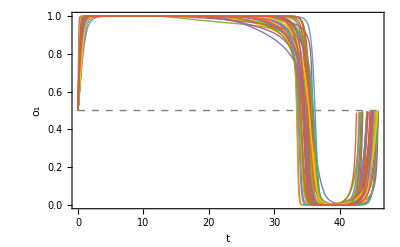
```mathematica
Show[-Graphics-,Graphics[{AbsoluteThickness[2],Line[{{0,0.5},{0,1},{32.8,1},{32.8,0},{41.953,0},{41.953,0.5}}]}]]
```

But only some of those leg motions are neurally-realizable with our neural model, architecture, and parameter constraints

```mathematica
ListPlot[MotorTimeTrajectory[Thread[{θ1,θ2,w11,w12,w21,w22,τ1,τ2}->#]]&/@F060,PlotStyle->AbsoluteThickness[1],Joined->True,Frame->True,FrameLabel->{t,Subscript[o, 1]},FrameStyle->Directive[Black,12],Prolog->{Gray,Dashed,Line[{{0,0.5},{100,0.5}}]}]
```

### The set of neural patterns or limit cycles that give rise to the biomechanically realizable leg motions

```mathematica
[
{{Show[
ListPlot[MotorTimeTrajectory[Thread[{θ1,θ2,w11,w12,w21,w22,τ1,τ2}->#]]&/@F060,PlotStyle->AbsoluteThickness[1],Joined->True,Frame->True,FrameLabel->{t,Subscript[o, 1]},FrameStyle->Directive[Black,12],Prolog->{Gray,Dashed,Line[{{0,0.5},{100,0.5}}]}],
Graphics[{AbsoluteThickness[2],Line[{{0,0.5},{0,1},{32.8,1},{32.8,0},{41.953,0},{41.953,0.5}}]}]]},
{ListPlot[InterneuronTimeTrajectory[Thread[{θ1,θ2,w11,w12,w21,w22,τ1,τ2}->#]]&/@F060,PlotStyle->AbsoluteThickness[1],Joined->True,Frame->True,FrameLabel->{t,Subscript[o, 2]},FrameStyle->Directive[Black,12]]}}]
```

### The set of neural parameters that give rise to those limit cycles

Neuron 1

```mathematica
T=ParallelTable[CAsymptoticFitness[{θ1->Θ1,w11->W11,w21->W21},250,1,0.01],{W21,-24,-3,0.025},{W11,7,24,0.025},{Θ1,-3.8,-2.4,0.005},Method->"CoarsestGrained"];
```

```mathematica
Show[
ListContourPlot3D[T,Contours->{0.6},DataRange->{{-3.8,-2.4},{7,24},{-24,-3}},Mesh->None,ContourStyle->Opacity[0.4],AxesLabel->{Subscript[θ, 1],Subscript[w, 11],Subscript[w, 21]},BoxStyle->Directive[Black,14]],
Graphics3D[{Green,AbsolutePointSize[5],Point[{θ1,w11,w21}/.Pis]}]]
```

Cross Weights

```mathematica
ContourPlot[CAsymptoticFitness[{w12->W12,w21->W21},250,1,0.001]==0.6,{W12,11.05,11.30},{W21,-13.3,-10.3},PlotPoints->25,MaxRecursion->3,ContourShading->None,FrameStyle->Directive[Black,12],FrameLabel->{Subscript[w, 12],Subscript[w, 21]},Epilog->{Darker[Green],AbsolutePointSize[6],Point[{w12,w21}/.Pis]}]
```

The Time Constants

```mathematica
ContourPlot[CAsymptoticFitness[{τ1->Τ1,τ2->Τ2},250,1,0.001]==0.6,{Τ1,0.3,0.9},{Τ2,7.25,9},PlotPoints->25,MaxRecursion->3,ContourShading->None,FrameStyle->Directive[Black,12],FrameLabel->{Subscript[τ, 1],Subscript[τ, 2]},Epilog->{Darker[Green],AbsolutePointSize[6],Point[{τ1,τ2}/.Pis]}]
```

## Figure 10

```mathematica
ContourPlot[CAsymptoticFitness[{θ1->Θ1,w11->W11},1000,1,0.001]==0.6,{Θ1,-3.4,-2.9},{W11,12,18},PlotPoints->50,MaxRecursion->3,FrameStyle->Directive[Black,12],FrameLabel->{Subscript[θ, 1],Subscript[w, 11]}]
```

```mathematica
L=;
```

```mathematica
NewR1=;
```

```mathematica
NewR2=;
```

```mathematica
Show[Graphics[{{Thickness[0.005],Line[L]},Red,Line[NewR1],Blue,Line[NewR2]}],PlotRange->{{-3.4,-2.9},{12,18}},PlotRangeClipping->True,AspectRatio->1,Frame->True,FrameStyle->{Black,12},FrameLabel->{Subscript[θ, 1],Subscript[w, 11]}]
```

```mathematica
L1=Take[L,{72,1164}];
L2=Take[L,{1165,1287}];
L3=Take[L,{1288,1448}];
L4=Join[Drop[L,1448],Take[L,71]];
```

```mathematica
T1=ParallelMap[Take[GaitParameters[Thread[{θ1,w11}->#]],3]&,L1];
T2=ParallelMap[Take[GaitParameters[Thread[{θ1,w11}->#]],3]&,L2];
T3=ParallelMap[Take[GaitParameters[Thread[{θ1,w11}->#]],3]&,L3];
T4=ParallelMap[Take[GaitParameters[Thread[{θ1,w11}->#]],3]&,L4];
```

```mathematica
FT1=Interpolation[MapIndexed[{(First[#2]-1)/(Length[T1]-1)//N,#1}&,T1]];
FT2=Interpolation[MapIndexed[{(First[#2]-1)/(Length[T2]-1)//N,#1}&,T2]];
FT3=Interpolation[MapIndexed[{(First[#2]-1)/(Length[T3]-1)//N,#1}&,T3]];
FT4=Interpolation[MapIndexed[{(First[#2]-1)/(Length[T4]-1)//N,#1}&,T4]];
```

```mathematica
Foo[ϕST_,ϕSW_,K_]:=
Module[{x = DistanceStar[ϕST,ϕSW]/K-TStar[ϕST,ϕSW]},
If[x < 0, I, x]]
```

```mathematica
Show[
Show[
Plot3D[{I,Foo[ϕST,ϕSW,0.60]},{ϕSW,-0.9947,-0.88},{ϕST,0,π/6},RegionFunction->Function[{x,y,z},x≥ArcTan[-4/3 Sec[y]]],Exclusions->None,PlotPoints->55,PlotRange->{{-0.9947,-0.88},All,{0,Automatic}},AxesEdge->{{1,-1},Automatic,{-1,1}},AxesStyle->Directive[Black,14],AxesLabel->{"ϕ_↑","ϕ_↓","ΔT"},Mesh->False,BoxRatios->{1,1,1},ViewPoint->{1.259, 2.934, 0.9}],PlotRange->{{-0.9947592804475792,-0.9279161241319434},{0.22482997736024501,0.5235987755982989},{8.603418555963638*^-19,1.9838132532608128}},PlotRangePadding->{{0.0013925657565757588,0.0013925657565757588},{0.006224349963292797,0.006224349963292797},{0.041329442776266934,0.041329442776266934}},PlotRegion->{{0.,1.},{0.,1.}},ViewCenter->{{0.5,0.5,0.5},{0.5,0.5}},ViewMatrix->{{{-9.470053423551827,2.4156183012291996,-0.002905774736667739,-10.004996237948209},{-4.22463100489291,-0.8053326486892137,0.4463211961671429,-4.202638960361999},{-9.936650274993347,-1.959795358366689,-0.18698700971206267,-5.316476394600656},{0.,0.,0.,1.}},{{2.0788683065601146,0.,0.5,0.},{0.,2.0788683065601146,0.5,0.},{0.,0.,2.4649015683271016,-6.095809781032571},{0.,0.,1.,0.}}},ViewPoint->{2.29503810941331,2.0232004480742947,1.2817554459617277},ViewProjection->"\"Perspective\"",ViewRange->Hold[NCache[All,{1.6857477317153071,3.768673090843304}]],ViewVector->{{-0.8015381282294953,1.0038697582145315,3.640618544482593},{-0.9613377022897613,0.37421437647927197,0.9919066266304064}},ViewVertical->{-0.29415382357910225,-0.25063361211536034,0.9223103168412472},ImagePadding->{{0.5000000000000003,34.74824186501888},{10.951821829853975,0.5}},ImageSize->{356.4026654443158,347.1370564328825}],Graphics3D[{Thick,Red,Line[Map[{#[[2]],#[[1]],#[[3]]}&,T1]],Line[Map[{#[[2]],#[[1]],#[[3]]}&,T2]],Line[Map[{#[[2]],#[[1]],#[[3]]}&,T3]],Line[Map[{#[[2]],#[[1]],#[[3]]}&,T4]]}],PlotRange->All]
```

This shows how each portion of the 0.6 fitness contour in (θ_1,w_11) neural parameter space maps onto the 0.6 fitness contour in gait space. We see that the degeneracy of three of the legs of the neural fitness contour are due to the gait space degeneracy, but one of them (brown) seems to arise from a degeneracy lower in the tower.

```mathematica
Show[
[
{{Plot[FT1[x][[1]],{x,0,1},PlotStyle->RGBColor[0.24, 0.6, 0.8],PlotRange->{{0,1},{0.35,0.53}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic},FrameLabel->{"s",Style["ϕ_↓",18,RGBColor[0.24, 0.6, 0.8]]}],
Plot[FT2[x][[1]],{x,0,1},PlotStyle->RGBColor[0.24, 0.6, 0.8],PlotRange->{{0,1},{0.35,0.53}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic}],
Plot[FT3[x][[1]],{x,0,1},PlotStyle->RGBColor[0.24, 0.6, 0.8],PlotRange->{{0,1},{0.35,0.53}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic}],
Plot[FT4[x][[1]],{x,0,1},PlotStyle->RGBColor[0.24, 0.6, 0.8],PlotRange->{{0,1},{0.35,0.53}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic}]},
{Plot[FT1[x][[2]],{x,0,1},PlotStyle->RGBColor[0.95, 0.627, 0.1425],PlotRange->{{0,1},{-1,-0.94}},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"s",Style["ϕ_↑",18,RGBColor[0.95, 0.627, 0.1425]]}],
Plot[FT2[x][[2]],{x,0,1},PlotStyle->RGBColor[0.95, 0.627, 0.1425],PlotRange->{{0,1},{-1,-0.94}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic}],
Plot[FT3[x][[2]],{x,0,1},PlotStyle->RGBColor[0.95, 0.627, 0.1425],PlotRange->{{0,1},{-1,-0.94}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic}],
Plot[FT4[x][[2]],{x,0,1},PlotStyle->RGBColor[0.95, 0.627, 0.1425],PlotRange->{{0,1},{-1,-0.94}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic}]},
{Plot[FT1[x][[3]],{x,0,1},PlotStyle->RGBColor[0.455, 0.7, 0.21],PlotRange->{{0,1},{0,2.04}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic},FrameLabel->{"s",Style["ΔT",18,RGBColor[0.455, 0.7, 0.21]]}],
Plot[FT2[x][[3]],{x,0,1},PlotStyle->RGBColor[0.455, 0.7, 0.21],PlotRange->{{0,1},{0,2.04}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic},FrameLabel->{"s",Style["ΔT",18,RGBColor[0.455, 0.7, 0.21]]}],
Plot[FT3[x][[3]],{x,0,1},PlotStyle->RGBColor[0.455, 0.7, 0.21],PlotRange->{{0,1},{0,2.04}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic},FrameLabel->{"s",Style["ΔT",18,RGBColor[0.455, 0.7, 0.21]]}],
Plot[FT4[x][[3]],{x,0,1},PlotStyle->RGBColor[0.455, 0.7, 0.21],PlotRange->{{0,1},{0,2.04}},Frame->True,FrameStyle->Directive[Black,12],FrameTicks->{None,Automatic},FrameLabel->{"s",Style["ΔT",18,RGBColor[0.455, 0.7, 0.21]]}]}}],
AspectRatio->1/GoldenRatio]
```

Now I need to explain these variations and constants in terms of the leg motion

Along L1), all gait parameters vary in a coordinated fashion. Thus, this branch of the 0.6 neural parameter contour is due to gait space degeneracy.

```mathematica
GraphicsGrid[
{{[
{{ListLinePlot[ParallelMap[BodyTimeTrajectory[Thread[{θ1,w11}->#]]&,L1],Frame->True,FrameLabel->{t,ϕ}]},
{ListLinePlot[ParallelMap[MotorTimeTrajectory[Thread[{θ1,w11}->#]]&,L1],Frame->True,FrameLabel->{t,Subscript[o, 1]}]}}],
ListLinePlot[{#[[1]]&/@T1,#[[2]]&/@T1,#[[3]]&/@T1},Frame->True,PlotLegends->{Style["ϕ_↓",RGBColor[0.24, 0.6, 0.8]],Style["ϕ_↑",RGBColor[0.95, 0.627, 0.1425]],Style["ΔT",RGBColor[0.455, 0.7, 0.21]]}]}}]
```

Along L2, all gait parameters vary in a coordinated fashion. Thus, this branch of the 0.6 neural parameter  contour is due to gait space degeneracy.

```mathematica
GraphicsGrid[
{{[
{{ListLinePlot[ParallelMap[BodyTimeTrajectory[Thread[{θ1,w11}->#]]&,L2],Frame->True,FrameLabel->{t,ϕ}]},
{ListLinePlot[ParallelMap[MotorTimeTrajectory[Thread[{θ1,w11}->#]]&,L2],Frame->True,FrameLabel->{t,Subscript[o, 1]}]}}],
ListLinePlot[{#[[1]]&/@T2,#[[2]]&/@T2,#[[3]]&/@T2},Frame->True,PlotLegends->{Style["ϕ_↓",RGBColor[0.24, 0.6, 0.8]],Style["ϕ_↑",RGBColor[0.95, 0.627, 0.1425]],Style["ΔT",RGBColor[0.455, 0.7, 0.21]]}]}}]
```

Along L3, ϕ_↓ is constant because it always hits the forward mechanical limit. Thus, this branch of the 0.6 neural parameter contour is due to a combination of gait space degeneracy and biomechanical degeneracy.

```mathematica
GraphicsGrid[
{{[
{{ListLinePlot[ParallelMap[MotorTimeTrajectory[Thread[{θ1,w11}->#]]&,L3],Frame->True,FrameStyle->Black,FrameLabel->{t,Subscript[o, 1]}]},
{ListLinePlot[ParallelMap[BodyTimeTrajectory[Thread[{θ1,w11}->#]]&,L3],Frame->True,FrameStyle->Black,FrameLabel->{t,ϕ}]}},
Spacings->{0,35}],
ListLinePlot[{#[[1]]&/@T3,#[[2]]&/@T3,#[[3]]&/@T3},Frame->True,PlotLegends->{Style["ϕ_↓",RGBColor[0.24, 0.6, 0.8]],Style["ϕ_↑",RGBColor[0.95, 0.627, 0.1425]],Style["ΔT",RGBColor[0.455, 0.7, 0.21]]}]}}]
```

```mathematica
ListLinePlot[ParallelMap[BodyTimeTrajectory[Thread[{θ1,w11}->#]]&,L3],Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{t,ϕ}]
```

Along L4, ϕ_↓ and ϕ_↑ are constant because they always hit the mechanical limits; ΔT is also constant.
Interestingly, the period stays the same even though the stance and swing durations are varying because they vary in a coordinated fashion.
Note that it looks like the step period varies because they hit the forward mechanical limit at different times, but they always wait the appropriate interval before stance.
Thus, this branch of the 0.6 neural parameter contour is due to a combination of biomechanical and neural degeneracy.

```mathematica
GraphicsGrid[
{{[
{{ListLinePlot[ParallelMap[BodyTimeTrajectory[Thread[{θ1,w11}->#]]&,L4],Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{t,ϕ}]},
{ListLinePlot[ParallelMap[MotorTimeTrajectory[Thread[{θ1,w11}->#]]&,L4],Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{t,Subscript[o, 1]}]}}],
ListLinePlot[{#[[1]]&/@T4,#[[2]]&/@T4,#[[3]]&/@T4},Frame->True,PlotLegends->{Style["ϕ_↓",RGBColor[0.24, 0.6, 0.8]],Style["ϕ_↑",RGBColor[0.95, 0.627, 0.1425]],Style["ΔT",RGBColor[0.455, 0.7, 0.21]]}]}}]
```